```mathematica
LastTwo[list_]:= Module[{},
If[Length[list]==1, Return[{list[[1]]}]];
Return[Take[list,-2]]
]
```

```mathematica
LastTwo[{1,2,3}]
```

{2,3}

```mathematica
CalcGoodForTuple[tuple_, count_, start_,max_] := Module[{sorted,fileName, file, current, index, dummy, range=1000, continue, distance,notZero,dTable, countNotZero},
(* always make sure the tuple is sorted *)
sorted = Sort[tuple];
countNotZero=Table[0,{p,tuple}];
fileName = FileNameForTuple[sorted];
index = 0;
current = start;

(* read any existing good values - actually read the last one and store it in the current variable.   Also increment the index variable *)
If [FileExistsQ[fileName],
Monitor[
continue = True;
file = OpenRead[fileName];
While[continue,
dummy = ReadList[file, Number, range];
index += Length[dummy];
If [Length[dummy] ≠ 0, current = Last[dummy]];
If [index ≥count, continue=False];
If[Length[dummy] ≠ range, continue = False];
];
Close[file];
current +=1;
,
"Reading existing " <> fileName <> " value " <> ToString[index]
]
];
current=Max[{current,start}];
If[current>max,Return[]];
(* now calculate good values and append them to the file for as long as the bound is not reached *)
(* If the process is aborted, the file is closed *)
file = OpenAppend[fileName, PageWidth->40000];
CheckAbort[
Monitor[
While[index < count,
dTable=ParallelTable[Distance[current, p], {p, sorted}];
notZero=Sort[Select[dTable,#≠0&]];
If[notZero=={},
distance=0,
countNotZero[[Length[notZero]]]++;
If[Length[notZero]==1,
distance=notZero[[1]],
distance = RandomInteger[Take[notZero,-2]]
]
];
If [distance == 0,
Write[file,current];
index +=1;
distance=1;
];
current += distance;
If[current>max,Break[]]
]
,
"Calculating good values " <> fileName <> ". " <> ToString[N[IntegerPart[(index / count) * 100000]/1000]] <> "%."<> "- " <> ToString[IntegerPart[Log[10,current]]] <> " (" <> ToString[countNotZero] <> ")" 
];
Close[file];
,
Print["Aborted at value : " <> ToString[index] ];
Close[file];
Abort[];
];
]
```

```mathematica
CalcGoodForTuple[{3,7,41,59}, 102, 0,100]
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\7\41\59\Solutions.txt.78.431%.-10335 ({0,0,0,157849})
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\7\41\59\Solutions.txt.78.431%.-10409 ({0,0,0,110110})
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\7\41\59\Solutions.txt.78.431%.-11310 ({0,0,0,859967})
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\7\41\59\Solutions.txt.78.431%.-11329 ({0,0,0,131088})
```

```mathematica
CloseStreams[]
```

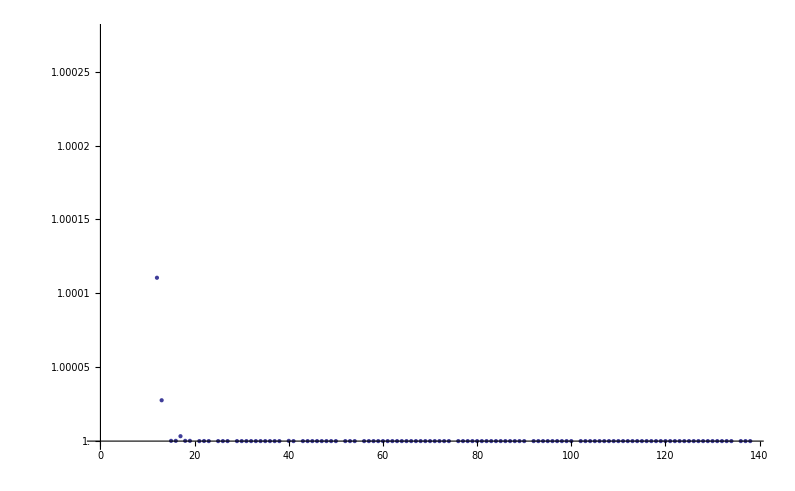

```mathematica
ListLogPlot[N[Ratios[Rest[ReadList[FileNameForTuple[{7,11,13,17}], Number,10000]]]]]
```